```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/gabriel.larios/Desktop/Fisica/7 PostDoc TAMU/0A Projects/[0] Warmups/CM_scan/Code/Potential_generator

```mathematica
V=ⅇ^((x1^2+x2^2-1)^2)
```

ⅇ^((-1+x1^2+x2^2)^2)

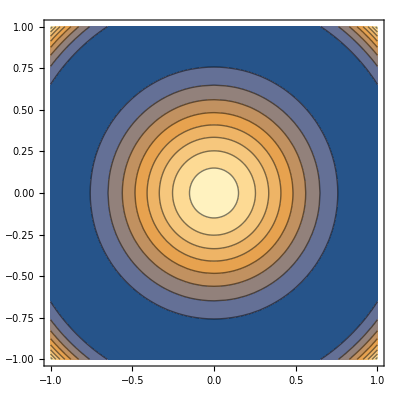

```mathematica
ContourPlot[V,{x1,-1,1},{x2,-1,1}]
```

#### Exporting into a python module

```mathematica
Import["https://raw.githubusercontent.com/zwicker-group/MathematicaToPython/master/ToPython.wl"]
```

```mathematica
pot=ToPython[V,NumpyPrefix->"np",Copy->True];
pot = StringReplace[pot,"np."->"tf."];
len = 2;
xs = StringRiffle[Table[StringJoin["x",ToString[ii]],{ii,len}],", "];
```

```mathematica
filename = "pot_expHiggs.py";
code = "
import tensorflow as tf
import numpy as np

dim = "<>ToString[len]<>"

def V(x):
    \"\"\"
	V = "<>pot<>"
    \"\"\"

    "<>xs<>" = tf.split(x, "<>ToString[len]<>", axis=1)

    return "<>pot;
```

```mathematica
file=OpenAppend[filename,PageWidth->Infinity];
WriteString[file,code]; 
Close[file];
```